### Adapting to a doubling rule with a minimal genetic algorithm

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

{<|Rule→{3926879090433,3,1},Fitness→-1|>,<|Rule→{6554501783280,3,1},Fitness→-1|>,<|Rule→{1920624470631,3,1},Fitness→-7|>,<|Rule→{5675243520663,3,1},Fitness→-11|>,<|Rule→{6307299722943,3,1},Fitness→-12|>,<|Rule→{2829072854472,3,1},Fitness→-3|>,<|Rule→{2979634402068,3,1},Fitness→0|>,<|Rule→{4563634923549,3,1},Fitness→-6|>,<|Rule→{1165938587640,3,1},Fitness→-10|>,<|Rule→{2970292860153,3,1},Fitness→-3|>,<|Rule→{413800411809,3,1},Fitness→-2|>,<|Rule→{6385903144155,3,1},Fitness→-5|>,<|Rule→{6819444899082,3,1},Fitness→-3|>,<|Rule→{5348159699034,3,1},Fitness→-2|>,<|Rule→{710358817746,3,1},Fitness→-10|>,<|Rule→{7592462753463,3,1},Fitness→-3|>,<|Rule→{772293430134,3,1},Fitness→-1|>,<|Rule→{945495086877,3,1},Fitness→-6|>,<|Rule→{6093979512612,3,1},Fitness→-3|>,<|Rule→{3571744000227,3,1},Fitness→-9|>,<|Rule→{3030567474123,3,1},Fitness→-1|>,<|Rule→{2611441754784,3,1},Fitness→-12|>,<|Rule→{982682688753,3,1},Fitness→-1|>,<|Rule→{2355169967730,3,1},Fitness→-2|>,<|Rule→{5099306955384,3,1},Fitness→-1|>,<|Rule→{6746040026274,3,1},Fitness→-5|>,<|Rule→{1746178104924,3,1},Fitness→0|>,<|Rule→{4924769985015,3,1},Fitness→-9|>,<|Rule→{6735900017514,3,1},Fitness→-2|>,<|Rule→{2979596143719,3,1},Fitness→-2|>,<|Rule→{6750480819330,3,1},Fitness→-9|>,<|Rule→{1669650223026,3,1},Fitness→-1|>,<|Rule→{847431107493,3,1},Fitness→-9|>,<|Rule→{961250551668,3,1},Fitness→-7|>,<|Rule→{1158930698598,3,1},Fitness→-14|>,<|Rule→{4258949460714,3,1},Fitness→-1|>,<|Rule→{7620091116636,3,1},Fitness→-10|>,<|Rule→{6547579595064,3,1},Fitness→-12|>,<|Rule→{496728169470,3,1},Fitness→0|>,<|Rule→{2751597432525,3,1},Fitness→-7|>,<|Rule→{460526981148,3,1},Fitness→-9|>,<|Rule→{3841984630710,3,1},Fitness→-6|>,<|Rule→{955844716440,3,1},Fitness→-2|>,<|Rule→{4642242816060,3,1},Fitness→-10|>,<|Rule→{3989581924131,3,1},Fitness→-1|>,<|Rule→{3730325746362,3,1},Fitness→-2|>,<|Rule→{7586589952836,3,1},Fitness→-1|>,<|Rule→{2330800140459,3,1},Fitness→-3|>,<|Rule→{7622725290498,3,1},Fitness→-1|>,<|Rule→{1044925764459,3,1},Fitness→-17|>,<|Rule→{5705709810129,3,1},Fitness→-12|>,<|Rule→{3135859809879,3,1},Fitness→-2|>,<|Rule→{2637177300816,3,1},Fitness→-11|>,<|Rule→{3310715756865,3,1},Fitness→-1|>,<|Rule→{310038868566,3,1},Fitness→-12|>,<|Rule→{3093186832047,3,1},Fitness→-8|>,<|Rule→{2037588260934,3,1},Fitness→-9|>,<|Rule→{5546573670615,3,1},Fitness→-9|>,<|Rule→{6261568072689,3,1},Fitness→-2|>,<|Rule→{5096982206712,3,1},Fitness→-2|>,<|Rule→{1560007658538,3,1},Fitness→-16|>,<|Rule→{261578886327,3,1},Fitness→-11|>,<|Rule→{3105599734968,3,1},Fitness→-1|>,<|Rule→{955974877056,3,1},Fitness→-9|>,<|Rule→{2316910876029,3,1},Fitness→-1|>,<|Rule→{1638097595694,3,1},Fitness→-1|>,<|Rule→{2513476390293,3,1},Fitness→-8|>,<|Rule→{4034859163716,3,1},Fitness→-9|>,<|Rule→{1276418664009,3,1},Fitness→-8|>,<|Rule→{145748293881,3,1},Fitness→-2|>,<|Rule→{6546284876835,3,1},Fitness→-3|>,<|Rule→{3723104389248,3,1},Fitness→-11|>,<|Rule→{1643626262622,3,1},Fitness→-3|>,<|Rule→{7397217752643,3,1},Fitness→-6|>,<|Rule→{3757598306877,3,1},Fitness→-15|>,<|Rule→{6304821414165,3,1},Fitness→0|>,<|Rule→{6791554363860,3,1},Fitness→-10|>,<|Rule→{695273579817,3,1},Fitness→-3|>,<|Rule→{364114004958,3,1},Fitness→-8|>,<|Rule→{4147440740835,3,1},Fitness→0|>,<|Rule→{3942992787822,3,1},Fitness→-6|>,<|Rule→{6241412883756,3,1},Fitness→-1|>,<|Rule→{5111694737832,3,1},Fitness→-1|>,<|Rule→{5598171779859,3,1},Fitness→-2|>,<|Rule→{1143974828985,3,1},Fitness→-5|>,<|Rule→{3066760862991,3,1},Fitness→-3|>,<|Rule→{423238329618,3,1},Fitness→-3|>,<|Rule→{5944085614620,3,1},Fitness→-14|>,<|Rule→{2538888414786,3,1},Fitness→-1|>,<|Rule→{6493968513774,3,1},Fitness→0|>,<|Rule→{6378805713528,3,1},Fitness→-10|>,<|Rule→{6639477784749,3,1},Fitness→-11|>,<|Rule→{890351338998,3,1},Fitness→-3|>,<|Rule→{3989938315212,3,1},Fitness→-10|>,<|Rule→{1149891732690,3,1},Fitness→-3|>,<|Rule→{3757175146386,3,1},Fitness→-8|>,<|Rule→{2494656399078,3,1},Fitness→-9|>,<|Rule→{101530623177,3,1},Fitness→-1|>,<|Rule→{1956681145848,3,1},Fitness→-2|>,<|Rule→{2686739544972,3,1},Fitness→-6|>,<|Rule→{859269285306,3,1},Fitness→-14|>,<|Rule→{1926184597365,3,1},Fitness→-3|>,<|Rule→{2934273661782,3,1},Fitness→-2|>,<|Rule→{4684180545342,3,1},Fitness→-10|>,<|Rule→{807319653225,3,1},Fitness→-6|>,<|Rule→{2826079970316,3,1},Fitness→-9|>,<|Rule→{3508894595580,3,1},Fitness→-2|>,<|Rule→{5989678627590,3,1},Fitness→-14|>,<|Rule→{3590686441098,3,1},Fitness→-4|>,<|Rule→{3025784103678,3,1},Fitness→-8|>,<|Rule→{5292314227578,3,1},Fitness→-3|>,<|Rule→{2119397752722,3,1},Fitness→-2|>,<|Rule→{2410540741866,3,1},Fitness→-10|>,<|Rule→{7234510237860,3,1},Fitness→-2|>,<|Rule→{6803096161374,3,1},Fitness→-14|>,<|Rule→{5642131305195,3,1},Fitness→0|>,<|Rule→{5642375180481,3,1},Fitness→0|>,<|Rule→{3187399622931,3,1},Fitness→-9|>,<|Rule→{673544442315,3,1},Fitness→-1|>,<|Rule→{3258126309873,3,1},Fitness→-9|>,<|Rule→{7135589104851,3,1},Fitness→-2|>,<|Rule→{602300964762,3,1},Fitness→-14|>,<|Rule→{2544522314625,3,1},Fitness→-12|>,<|Rule→{3829512917844,3,1},Fitness→-12|>,<|Rule→{6349900062588,3,1},Fitness→-2|>,<|Rule→{2794311796149,3,1},Fitness→-11|>,<|Rule→{5841040167501,3,1},Fitness→-4|>,<|Rule→{3452173635708,3,1},Fitness→-12|>,<|Rule→{3400054616475,3,1},Fitness→-2|>,<|Rule→{726600369234,3,1},Fitness→-9|>,<|Rule→{3738783047481,3,1},Fitness→-12|>,<|Rule→{4480721839017,3,1},Fitness→-16|>,<|Rule→{3940585739739,3,1},Fitness→-8|>,<|Rule→{6394310422839,3,1},Fitness→-8|>,<|Rule→{4718214167646,3,1},Fitness→-2|>,<|Rule→{6612633639981,3,1},Fitness→-3|>,<|Rule→{4194169016949,3,1},Fitness→-2|>,<|Rule→{2939140622304,3,1},Fitness→-10|>,<|Rule→{3781394694180,3,1},Fitness→-6|>,<|Rule→{4478388185478,3,1},Fitness→-3|>,<|Rule→{4090718057193,3,1},Fitness→-7|>,<|Rule→{1834644175857,3,1},Fitness→-6|>,<|Rule→{1479744800340,3,1},Fitness→-6|>,<|Rule→{5172453096921,3,1},Fitness→-13|>,<|Rule→{4726479304290,3,1},Fitness→-2|>,<|Rule→{6417102602778,3,1},Fitness→-3|>,<|Rule→{165217320357,3,1},Fitness→-7|>,<|Rule→{3405585835914,3,1},Fitness→-3|>,<|Rule→{2612039334180,3,1},Fitness→-6|>,<|Rule→{3618528581526,3,1},Fitness→-3|>,<|Rule→{3687222831480,3,1},Fitness→-8|>,<|Rule→{2493089586438,3,1},Fitness→-7|>,<|Rule→{7450691053764,3,1},Fitness→-2|>,<|Rule→{1436744808792,3,1},Fitness→-15|>,<|Rule→{6359058638694,3,1},Fitness→-11|>,<|Rule→{5500282694571,3,1},Fitness→-2|>,<|Rule→{3868648681017,3,1},Fitness→-5|>,<|Rule→{6645831331242,3,1},Fitness→-8|>,<|Rule→{3530512320339,3,1},Fitness→-2|>,<|Rule→{2442339389466,3,1},Fitness→0|>,<|Rule→{3077929239492,3,1},Fitness→-13|>,<|Rule→{1203535307010,3,1},Fitness→-2|>,<|Rule→{2930656552380,3,1},Fitness→-6|>,<|Rule→{3853607205876,3,1},Fitness→-8|>,<|Rule→{3725463027267,3,1},Fitness→-10|>,<|Rule→{5002839311934,3,1},Fitness→-1|>,<|Rule→{2914534289799,3,1},Fitness→-3|>,<|Rule→{2666866315626,3,1},Fitness→-3|>,<|Rule→{153426212694,3,1},Fitness→-13|>,<|Rule→{1236158701755,3,1},Fitness→-7|>,<|Rule→{357567462780,3,1},Fitness→-6|>,<|Rule→{7181036663139,3,1},Fitness→-13|>,<|Rule→{3239806653975,3,1},Fitness→-5|>,<|Rule→{2857034165265,3,1},Fitness→-9|>,<|Rule→{5605148743755,3,1},Fitness→-2|>,<|Rule→{3996560625576,3,1},Fitness→-2|>,<|Rule→{4462136783454,3,1},Fitness→-10|>,<|Rule→{3800918634075,3,1},Fitness→-11|>,<|Rule→{968338748757,3,1},Fitness→-10|>,<|Rule→{2967148079775,3,1},Fitness→-10|>,<|Rule→{1307766702444,3,1},Fitness→-9|>,<|Rule→{5760834811911,3,1},Fitness→-8|>,<|Rule→{3785668668342,3,1},Fitness→-14|>,<|Rule→{4293744323691,3,1},Fitness→-8|>,<|Rule→{5631881119086,3,1},Fitness→-2|>,<|Rule→{200117192955,3,1},Fitness→-8|>,<|Rule→{3191122930194,3,1},Fitness→0|>,<|Rule→{4407624336237,3,1},Fitness→-1|>,<|Rule→{786317691969,3,1},Fitness→0|>,<|Rule→{6174501282684,3,1},Fitness→-4|>,<|Rule→{6091471578009,3,1},Fitness→-5|>,<|Rule→{3886790893149,3,1},Fitness→-5|>,<|Rule→{4193877234771,3,1},Fitness→-1|>,<|Rule→{3868798576041,3,1},Fitness→-13|>,<|Rule→{2714608498482,3,1},Fitness→-9|>,<|Rule→{36166577667,3,1},Fitness→-9|>,<|Rule→{4101707668635,3,1},Fitness→-10|>,<|Rule→{7507244759682,3,1},Fitness→-8|>,<|Rule→{4267334014353,3,1},Fitness→-1|>,<|Rule→{3086399054865,3,1},Fitness→-2|>}

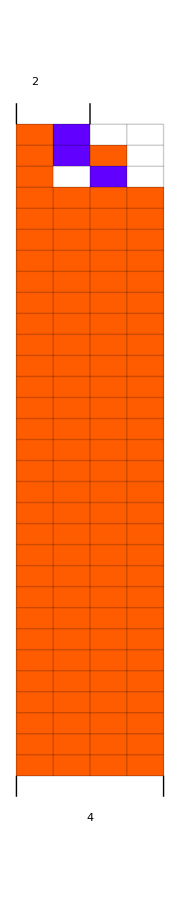
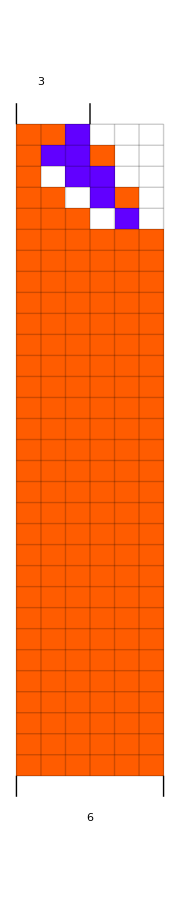
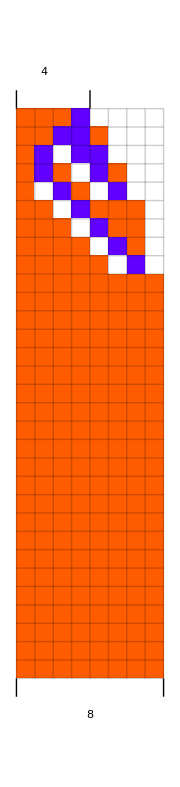
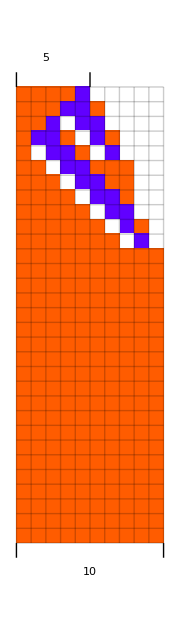
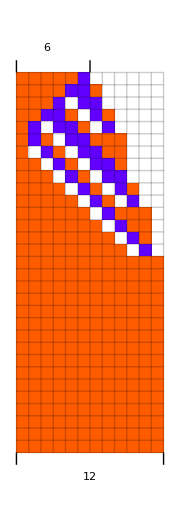
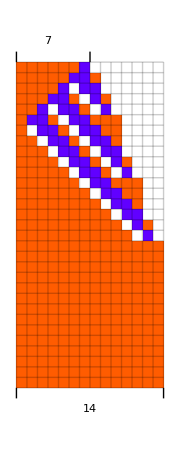
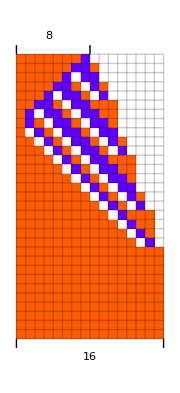
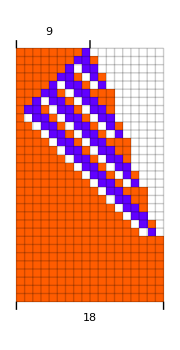

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2], ImageSize->Small],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{i+1, Length[ca]},{i+1, Length[ca] + 1}}], Style[Text[ToString[i+1], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&@ [[SelectFirst[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]]]]
```

#### Looking at evolution history

```mathematica
SelectFirst[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]
```

160

```mathematica
SeedRandom[221350 + 160];AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>]
```

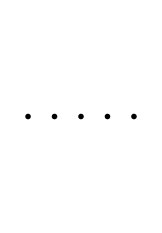
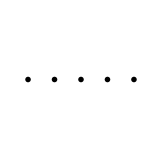
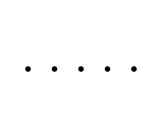
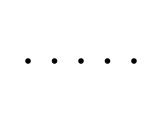
{-Graphics--16,-Graphics--15,-Graphics--11,-Graphics--3,-Graphics--1,-Graphics-0}

```mathematica
Labeled[With[{cas = Table[CellularAutomaton[#Rule,{Append[Table[1, j], 2], 0}, 25], {j, 7}]},GraphicsRow[Table[Show[ArrayPlot[cas[[i]], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2], ImageSize->30],
Graphics[{Line[{{0, Length[cas[[i]]]},{0, Length[cas[[i]]] + 1}}],Line[{{i+1, Length[cas[[i]]]},{i+1, Length[cas[[i]]] + 1}}], Style[Text[ToString[i+1], {i/2, Length[cas[[i]]] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[cas[[i]]]], 1]),
Style[Text[ToString[Count[Last[cas[[i]]], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[cas[[i]]]], 1]], -2}],10]
}], PlotRange->All], {i,3, 7}]]], Style[Text[#Fitness], 10], Frame->True]&/@ GatherBy[, #Fitness&][[{3, 4, 5, 8, 9, 10}, -1]]
```

```mathematica
ResourceFunction["Progressive"]
```

```mathematica
ListStepPlot[MapIndexed[Block[{ca = CellularAutomaton[#Rule,{Append[Table[1, 5], 2], 0}, 60], loss}, 
loss = Abs[Count[Last[ca], 1] - 9];If[MemberQ[, Last[#2]], Callout[loss, ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], LabelVisibility->All], loss]]&,], PlotRange->All, LabelingSize->50]
```